#### with

```mathematica
CoupledEntropy[CoupledNormalDistribution[0., 1., 1], #, 2, 1, {-∞, ∞}, False]&/@{0.01,0.25,0.5,1,2,4}
```

{2.53688,2.65255,2.69962,2.64159,2.33066,1.76479}

```mathematica
CoupledEntropy[CoupledNormalDistribution[0.,1.,1],#,2,1,{-∞,∞},True]&/@{0.01,0.25,0.5,1,2,4}
```

{2.14481,2.11442,2.08107,1.99952,1.82768,1.55801}

```mathematica
TsallisEntropy[CoupledNormalDistribution[0.,1.,1],#,2,1,{-∞,∞},False]&/@{0.01,0.25,0.5,1,2,4}
```

{2.43852,1.42532,1.09455,0.840845,0.677344,0.583659}

```mathematica
TsallisEntropy[CoupledNormalDistribution[0.,1.,1],#,2,1,{-∞,∞},True]&/@{0.01,0.25,0.5,1,2,4}
```

{2.56225,3.31568,4.04943,5.28319,6.99198,8.82395}

```mathematica
Clear[PlotCoupledEntDist]
```

```mathematica
Solve[(1 + d κMod)/(-α κMod)==((1+d κOrg)/(-α κOrg))(1-(-α κBias)/(1+ d κBias)),κMod,Reals]//FullSimplify
```

{{κMod→(κOrg+d κBias κOrg)/(1+κBias (d+α+d α κOrg))}}

```mathematica
$Assumptions=$Assumptions&&-1<a<1&&-1<b<1&&-1<c<1&&-1<d<1
```

(μ1|μ2|σ|κ|a|b|c|d)∈ℝ&&0<σ<∞&&0<κ<∞&&-∞<{μ1,μ2}<∞&&-1<a<1&&-1<b<1&&-1<c<1&&-1<d<1

```mathematica
{{d,e},{0,f}}//MatrixForm
```

(d | e
0 | f)

```mathematica
Matrix2x2 = {{a,0},{b,c}}.{{d,e},{0,f}}//FullSimplify;
(*Matrix2x2=Table[RandomReal[{-1,1}],{2},{2}]*)
MatrixPD = ConjugateTranspose[Matrix2x2].Matrix2x2//FullSimplify;
PositiveDefiniteMatrixQ[MatrixPD]
```

False

```mathematica
MatrixPD//FullSimplify
```

{{(a^2+b^2) d^2,(a^2+b^2) d e+b c d f},{(a^2+b^2) d e+b c d f,a^2 e^2+(b e+c f)^2}}

```mathematica
Inverse[Matrix2x2]
```

{{(b e+c f)/(a c d f),-e/(c d f)},{-b/(a c f),1/(c f)}}

```mathematica
Repaclet:ref/Re[Conjugatepaclet:ref/Conjugate[{x1,x2}].MatrixPD.{x1,x2}]
```

RefLink[Re,paclet:ref/Re][RefLink[Conjugate,paclet:ref/Conjugate][{x1,x2}].{(a^2+b^2) d^2 x1+((a^2+b^2) d e+b c d f) x2,((a^2+b^2) d e+b c d f) x1+(a^2 e^2+(b e+c f)^2) x2}]

```mathematica
Conjugate[{x1,x2}].MatrixPositiveDefinite.{x1,x2}
```

x1 ((a Conjugate[a]+c Conjugate[c]) Conjugate[x1]+(a Conjugate[b]+c Conjugate[d]) Conjugate[x2])+x2 ((b Conjugate[a]+d Conjugate[c]) Conjugate[x1]+(b Conjugate[b]+d Conjugate[d]) Conjugate[x2])

```mathematica
Assuming[{a,b,c,d}∈Reals,x1 ((a Conjugate[a]+c Conjugate[c]) Conjugate[x1]+(a Conjugate[b]+c Conjugate[d]) Conjugate[x2])+x2 ((b Conjugate[a]+d Conjugate[c]) Conjugate[x1]+(b Conjugate[b]+d Conjugate[d]) Conjugate[x2])]//FullSimplify
```

```mathematica
(a^2 x1+a b x2+c (c x1+d x2)) x1+(a b x1+c d x1+(b^2+d^2) x2) x2//Simplify
```

a^2 x1^2+c^2 x1^2+2 a b x1 x2+2 c d x1 x2+(b^2+d^2) x2^2

```mathematica
PositiveDefiniteMatrixQ[{{20,30},{30,45}}]
```

False

```mathematica
Inverse[{{2,3},{4,6}}]
```

Inverse::sing: Matrix {{2,3},{4,6}} is singular.

Inverse[{{2,3},{4,6}}]

```mathematica
Clear[TableCoupledEntDist];
TableCoupledEntDist[]:=
Module[{coupledDist},
coupledDist=CoupledNormalDistribution[0.,1.,κ];
Table[
{
CoupledEntropy[coupledDist,κ,1,1,{-∞,∞},False,False], (* α = 1; ie no root *)
CoupledEntropy[coupledDist,κ,2,1,{-∞,∞},False,False], (* α = 2; ie with root *)
CoupledEntropy[coupledDist,0,1,1,{-∞,∞},False,False] (* Shannon *)
(*TsallisEntropy[coupledDist,κ,α,1,{-∞,∞},False],
TsallisEntropy[coupledDist,κ,α,1,{-∞,∞},True],*)
},{κ,0,4,.2}
]
]
```

```mathematica
TableCoupledEntDist[]
```

{{1.41894,1.64744,1.41894},{1.48983,1.73997,1.6275},{1.56397,1.81883,1.84776},{1.63843,1.88696,2.07371},{1.71199,1.94663,2.30203},{1.78416,1.99952,2.53102},{1.85476,2.04686,2.7598},{1.92376,2.08957,2.98792},{1.99116,2.12838,3.21517},{2.05704,2.16384,3.44144},{2.12146,2.19642,3.66673},{2.18448,2.22649,3.89103},{2.24618,2.25434,4.11439},{2.30664,2.28024,4.33685},{2.3659,2.3044,4.55844},{2.42403,2.32701,4.77924},{2.4811,2.34821,4.99927},{2.53714,2.36815,5.21859},{2.59222,2.38694,5.43723},{2.64638,2.40469,5.65525},{2.69965,2.42149,5.87267}}

```mathematica
Table[CoupledLogarithm[x,κ,1],
{x,0.02,2,0.02},
{κ,{0,0.5,1.0}}
]//MatrixForm
```

(-3.91202 | -1.45712 | -0.858579
-3.21888 | -1.31601 | -0.8
-2.81341 | -1.21703 | -0.755051
-2.52573 | -1.13823 | -0.717157
-2.30259 | -1.07168 | -0.683772
-2.12026 | -1.01352 | -0.65359
-1.96611 | -0.961501 | -0.625834
-1.83258 | -0.914233 | -0.6
-1.7148 | -0.870757 | -0.575736
-1.60944 | -0.830393 | -0.552786
-1.51413 | -0.792638 | -0.530958
-1.42712 | -0.757107 | -0.510102
-1.34707 | -0.723499 | -0.490098
-1.27297 | -0.691573 | -0.47085
-1.20397 | -0.661134 | -0.452277
-1.13943 | -0.632019 | -0.434315
-1.07881 | -0.604094 | -0.416905
-1.02165 | -0.577243 | -0.4
-0.967584 | -0.551369 | -0.383559
-0.916291 | -0.526387 | -0.367544
-0.867501 | -0.502226 | -0.351926
-0.820981 | -0.478819 | -0.336675
-0.776529 | -0.456111 | -0.321767
-0.733969 | -0.434053 | -0.30718
-0.693147 | -0.412599 | -0.292893
-0.653926 | -0.39171 | -0.27889
-0.616186 | -0.371349 | -0.265153
-0.579818 | -0.351486 | -0.251669
-0.544727 | -0.33209 | -0.238423
-0.510826 | -0.313135 | -0.225403
-0.478036 | -0.294596 | -0.212599
-0.446287 | -0.276452 | -0.2
-0.415515 | -0.258682 | -0.187596
-0.385662 | -0.241268 | -0.175379
-0.356675 | -0.224192 | -0.16334
-0.328504 | -0.207438 | -0.151472
-0.301105 | -0.190992 | -0.139767
-0.274437 | -0.174839 | -0.12822
-0.248461 | -0.158967 | -0.116824
-0.223144 | -0.143364 | -0.105573
-0.198451 | -0.12802 | -0.0944615
-0.174353 | -0.112922 | -0.0834849
-0.150823 | -0.0980629 | -0.0726382
-0.127833 | -0.0834321 | -0.0619168
-0.105361 | -0.0690212 | -0.0513167
-0.0833816 | -0.0548223 | -0.0408337
-0.0618754 | -0.0408278 | -0.030464
-0.040822 | -0.0270303 | -0.0202041
-0.0202027 | -0.0134232 | -0.0100505
0. | 0. | 0.
0.0198026 | 0.0132454 | 0.00995049
0.0392207 | 0.0263188 | 0.0198039
0.0582689 | 0.0392256 | 0.029563
0.076961 | 0.0519711 | 0.0392305
0.0953102 | 0.0645602 | 0.0488088
0.113329 | 0.0769976 | 0.0583005
0.131028 | 0.0892879 | 0.0677078
0.14842 | 0.101435 | 0.077033
0.165514 | 0.113444 | 0.086278
0.182322 | 0.125317 | 0.0954451
0.198851 | 0.137059 | 0.104536
0.215111 | 0.148674 | 0.113553
0.231112 | 0.160165 | 0.122497
0.24686 | 0.171534 | 0.131371
0.262364 | 0.182786 | 0.140175
0.277632 | 0.193923 | 0.148913
0.29267 | 0.204948 | 0.157584
0.307485 | 0.215863 | 0.16619
0.322083 | 0.226673 | 0.174734
0.336472 | 0.237378 | 0.183216
0.350657 | 0.247982 | 0.191638
0.364643 | 0.258486 | 0.2
0.378436 | 0.268894 | 0.208305
0.392042 | 0.279208 | 0.216553
0.405465 | 0.289428 | 0.224745
0.41871 | 0.299559 | 0.232883
0.431782 | 0.309601 | 0.240967
0.444686 | 0.319556 | 0.249
0.457425 | 0.329427 | 0.256981
0.470004 | 0.339214 | 0.264911
0.482426 | 0.348921 | 0.272792
0.494696 | 0.358547 | 0.280625
0.506818 | 0.368096 | 0.28841
0.518794 | 0.377569 | 0.296148
0.530628 | 0.386966 | 0.30384
0.542324 | 0.396291 | 0.311488
0.553885 | 0.405543 | 0.319091
0.565314 | 0.414724 | 0.32665
0.576613 | 0.423837 | 0.334166
0.587787 | 0.432881 | 0.341641
0.598837 | 0.441858 | 0.349074
0.609766 | 0.45077 | 0.356466
0.620576 | 0.459618 | 0.363818
0.631272 | 0.468402 | 0.371131
0.641854 | 0.477125 | 0.378405
0.652325 | 0.485786 | 0.385641
0.662688 | 0.494387 | 0.392839
0.672944 | 0.50293 | 0.4
0.683097 | 0.511414 | 0.407125
0.693147 | 0.519842 | 0.414214)

```mathematica
coupledDistTest=CoupledNormalDistribution[0.,1.,κ];
Table[
{
CoupledEntropy[coupledDistTest,κ,1,2,1,{-∞,∞}], (* α = 1; ie no root *)
CoupledEntropy[coupledDistTest,κ,1,2,2,{-∞,∞}], (* α = 2; ie with root *)
CoupledEntropy[coupledDistTest,0,1,2,1,{-∞,∞}] (* Shannon *)
(*TsallisEntropy[coupledDist,κ,α,1,{-∞,∞},False],
TsallisEntropy[coupledDist,κ,α,1,{-∞,∞},True],*)
},
{κ,0,2,1}
]
```

{{1.41246,1.16405,1.41246},{1.05216,0.952939,2.51338},{0.998084,0.872521,3.65441}}

```mathematica
CoupledCrossEntropy[ProbabilityDistribution[0.3989422804014327/(√(ⅇ^(1. (0.+x)^2))),{x,-∞,∞}],ProbabilityDistribution[0.3989422804014327/(√(ⅇ^(1. (0.+x)^2))),{x,-∞,∞}],0,1,1,1,{-∞,∞}]
```

CoupledCrossEntropy[ProbabilityDistribution[0.398942/(√(ⅇ^(1. (0.+x)^2))),{x,-∞,∞}],ProbabilityDistribution[0.398942/(√(ⅇ^(1. (0.+x)^2))),{x,-∞,∞}],0,1,1,1,{-∞,∞}]

```mathematica
NIntegrate[CoupledProbability[ProbabilityDistribution[0.3989422804014327/(√(2.718281828459045^(1. (0.+x)^2))),{x,-∞,∞}],(-2 1)/(1+1 1),x] CoupledLogarithm[PDF[ProbabilityDistribution[0.3989422804014327/(√(2.718281828459045^(1. (0.+x)^2))),{x,-∞,∞}],x]^-2,1,1]^(1/1),{x,-∞,∞},
Method->"AdaptiveMonteCarlo"]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. (y^2)^(-System`MeijerGDump`s$5833) ComplexInfinity Gamma[System`MeijerGDump`s$5833] encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. (y^2)^(-System`MeijerGDump`s$5833) ComplexInfinity encountered.

2.60798

```mathematica
?CoupledCrossEntropy
```

```mathematica
CoupledEntropy[coupledDistTest,κ,1,2,1,{-∞,∞}]
```

```mathematica
coupledDistTest/.κ->2
```

ProbabilityDistribution[0.269676/(√((1+2. (0.+x)^2)^(3/2))),{x,-∞,∞}]

```mathematica
CoupledCrossEntropy[ProbabilityDistribution[0.3989422804014327/(√(ⅇ^(1. (0.+x)^2))),{x,-∞,∞}],ProbabilityDistribution[0.3989422804014327/(√(ⅇ^(1. (0.+x)^2))),{x,-∞,∞}],0,2,1,1,{-∞,∞}]//N
```

CoupledCrossEntropy[ProbabilityDistribution[0.398942/(√(2.71828^(1. (0.+x)^2))),{x,-∞,∞}],ProbabilityDistribution[0.398942/(√(2.71828^(1. (0.+x)^2))),{x,-∞,∞}],0.,2.,1.,1.,{-∞,∞}]

```mathematica
CoupledCrossEntropy[
```

```mathematica
CoupledEntropy[coupledDistTest,κ,1,2,1,{-∞,∞}]/.κ->1
```

CoupledCrossEntropy[ProbabilityDistribution[0.31831/(√((1+1. (0.+x)^2)^2)),{x,-∞,∞}],ProbabilityDistribution[0.31831/(√((1+1. (0.+x)^2)^2)),{x,-∞,∞}],1,2,1,1,{-∞,∞}]

```mathematica
f[x_,y_]:=x^2 y;
f[2,y_]:=4y;
```

```mathematica
?f
```

```mathematica
f[2,j]
```

4 j

```mathematica
?CoupledEntropyTemp
```

```mathematica
coupledDist=CoupledNormalDistribution[0,1,κ];
Table[
NCoupledEntropy[coupledDist,κ],
{κ,{0,0.2,0.4,0.6,0.8,1.0}}
]
```

{1.43206,1.25486,1.17261,1.10647,1.08678,1.06624}

Removed 1/alpha power from pdf in coupled log

```mathematica
coupledDist=CoupledNormalDistribution[0,1,κ];
Table[
NCoupledEntropy[coupledDist,κ],
{κ,{0,0.2,0.4,0.6,0.8,1.0}}
]
```

{1.42266,1.25585,1.15984,1.10514,1.05696,1.05878}

```mathematica
Table[
NIntegrate[PDF[coupledDist,x],{x,-∞,∞}],
{κ,{0,0.5,1}}
]
```

{1.,1.,1.}

```mathematica
CoupledProbability[coupledDist,(-α κ)/(1+ κ),x]CoupledLogarithm[PDF[coupledDist,x]^-α,κ,1]//FullSimplify
```

((1+x^2 κ)^(-(1+κ+α κ)/(2 κ)) (-1+(π^(α/2) (((1+x^2 κ)^(1+1/κ))/κ)^(α/2) (Gamma[1/(2 κ)]/Gamma[(1+κ)/(2 κ)])^α)^(κ/(1+κ))) Gamma[(1+κ+α κ)/(2 κ)])/(√π √κ Gamma[(1+α κ)/(2 κ)])

```mathematica
((1+x^2 κ)^(-(1+κ+α κ)/(2 κ)) (-1+(π^(α/2) (((1+x^2 κ)^(1+1/κ))/κ)^(α/2) (Gamma[1/(2 κ)]/Gamma[(1+κ)/(2 κ)])^α)^(κ/(1+κ))) Gamma[(1+κ+α κ)/(2 κ)])/(√π √κ Gamma[(1+α κ)/(2 κ)])/.α->2//FullSimplify
```

((1+x^2 κ)^(-(1+3 κ)/(2 κ)) Gamma[1/2 (3+1/κ)] (-1+π^(κ/(1+κ)) (((1+x^2 κ)^(1+1/κ) Gamma[1/(2 κ)]^2)/(κ Gamma[(1+κ)/(2 κ)]^2))^(κ/(1+κ))))/(√π √κ Gamma[1+1/(2 κ)])

```mathematica
Table[
NIntegrate[((1+x^2 κ)^(-(1+3 κ)/(2 κ)) Gamma[1/2 (3+1/κ)] (-1+π^(κ/(1+κ)) (((1+x^2 κ)^(1+1/κ) Gamma[1/(2 κ)]^2)/(κ Gamma[(1+κ)/(2 κ)]^2))^(κ/(1+κ))))/(√π √κ Gamma[1+1/(2 κ)]),{x,-∞,∞}],
{κ,{10^-6,0.2,0.4,0.6,0.8,1.0}}
]
```

{2.83788,3.28654,3.75699,4.24788,4.75724,5.28319}

```mathematica
Table[
NIntegrate[1/2((1+x^2 κ)^(-(1+3 κ)/(2 κ)) Gamma[1/2 (3+1/κ)] (-1+π^(κ/(1+κ)) (((1+x^2 κ)^(1+1/κ) Gamma[1/(2 κ)]^2)/(κ Gamma[(1+κ)/(2 κ)]^2))^(κ/(1+κ))))/(√π √κ Gamma[1+1/(2 κ)]),{x,-∞,∞}],
{κ,{10^-6,0.2,0.4,0.6,0.8,1.0}}
]
```

{1.41894,1.64327,1.8785,2.12394,2.37862,2.64159}

```mathematica
Table[
Integrate[1/2((1+x^2 κ)^(-(1+3 κ)/(2 κ)) Gamma[1/2 (3+1/κ)] (-1+π^(κ/(1+κ)) (((1+x^2 κ)^(1+1/κ) Gamma[1/(2 κ)]^2)/(κ Gamma[(1+κ)/(2 κ)]^2))^(κ/(1+κ))))/(√π √κ Gamma[1+1/(2 κ)]),{x,-∞,∞}],
{κ,{10^-6,0.2,0.4,0.6,0.8,1.0}}
]
```

$Aborted

```mathematica
Table[
NIntegrate[1/2((1+x^2 κ)^(-(1+3 κ)/(2 κ)) Gamma[1/2 (3+1/κ)] (-1+π^(κ/(1+κ)) (((1+x^2 κ)^(1+1/κ) Gamma[1/(2 κ)]^2)/(κ Gamma[(1+κ)/(2 κ)]^2))^(κ/(1+κ))))/(√π √κ Gamma[1+1/(2 κ)]),{x,-∞,∞},
Method->"AdaptiveMonteCarlo"],
{κ,{10^-6,0.2,0.4,0.6,0.8,1.0}}
]
```

{1.4209,1.64358,1.91882,2.11614,2.38222,2.65497}

Using NCoupledProbability in the NCoupledEntropy Function

```mathematica
coupledDist=CoupledNormalDistribution[0,1,κ];
Table[
NCoupledEntropy[coupledDist,κ],
{κ,{0,0.2,0.4,0.6,0.8,1.0}}
]
```

{1.43,1.25272,1.17519,1.10744,1.09851,1.05728}

Using FullSimplify in the NCoupledEntropy Function

```mathematica
coupledDist=CoupledNormalDistribution[0,1,κ];
Table[
NCoupledEntropy[coupledDist,κ],
{κ,{0,0.2,0.4,0.6,0.8,1.0}}
]
```

FullSimplify::fas: Warning: one or more assumptions evaluated to False.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in x near {x} = {0.998241}. NIntegrate obtained 107358. and 91910. for the integral and error estimates.

{107358.,1.25552,1.16055,1.12289,1.07665,1.045}

```mathematica
coupledDist=CoupledNormalDistribution[0,1,κ];
Table[
NCoupledEntropy[coupledDist,κ],
{κ,{0,0.2,0.4,0.6,0.8,1.0}}
]
```

FullSimplify::fas: Warning: one or more assumptions evaluated to False.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in x near {x} = {0.998458}. NIntegrate obtained 22378.3 and 6913.14 for the integral and error estimates.

{22378.3,1.66135,1.88184,2.14227,2.4144,2.65415}

```mathematica
FullSimplify[CoupledEntropy[CoupledNormalDistribution[0,1,κ],0]]
```

∫_(-∞)^∞ (Gamma[(1+κ)/(2 κ)] Log[(π (1+x^2 κ)^(1+1/κ) Gamma[1/(2 κ)]^2)/(κ Gamma[(1+κ)/(2 κ)]^2)])/(2 √π √(((1+x^2 κ)^(1+1/κ))/κ) Gamma[1/(2 κ)])ⅆx

```mathematica
(Gamma[(1+κ)/(2 κ)] Log[(π (1+x^2 κ)^(1+1/κ) Gamma[1/(2 κ)]^2)/(κ Gamma[(1+κ)/(2 κ)]^2)])/(2 √π √(((1+x^2 κ)^(1+1/κ))/κ) Gamma[1/(2 κ)])//FullSimplify
```

(Gamma[(1+κ)/(2 κ)] Log[(π (1+x^2 κ)^(1+1/κ) Gamma[1/(2 κ)]^2)/(κ Gamma[(1+κ)/(2 κ)]^2)])/(2 √π √(((1+x^2 κ)^(1+1/κ))/κ) Gamma[1/(2 κ)])

```mathematica
CoupledEntropy[CoupledNormalDistribution[0,1,0],κ]
```

ConditionalExpression[1/2 (1+Log[2]+Log[π]), κ==0]

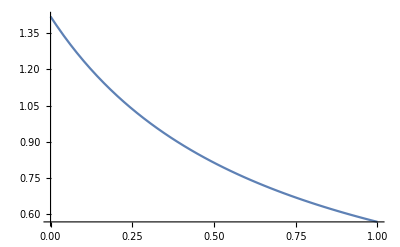

```mathematica
Plot[(-1+(2 π)^(κ/(2+4 κ)) √((1+3 κ)/(1+2 κ)))/κ,{κ,0,1}]
```

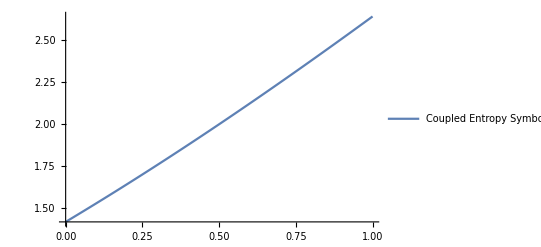

```mathematica
Plot[
-(κ-π^(κ/(1+κ)) κ^(1/(1+κ)) (1+κ) (Gamma[1/(2 κ)]/Gamma[(1+κ)/(2 κ)])^((2 κ)/(1+κ)))/(2 κ^2),
{κ,0,1},
PlotRange->Full,
PlotLegends->{"Coupled Entropy Symbolic"}
]
```

```mathematica
ClearAll[CoupledCrossEntropy];
CoupledCrossEntropy[distP_,distQ_,κ_,d_:1,α_:2, δ_:1,limits_:{-∞,∞}]:=CoupledCrossEntropy[distP,distQ,κ,d,α,δ,limits]=Integrate[FullSimplify[
CoupledProbability[distP,(-α κ)/(1+d κ),x](1/α CoupledLogarithm[PDF[distQ,x]^-α,κ,d])^(1/δ)
],{x,limits⟦1⟧,limits⟦2⟧}
]
```

```mathematica
ClearAll[CoupledEntropy];
CoupledEntropy[dist_,κ_,d_:1,α_:2,δ_:1,limits_:{-∞,∞}]:=
CoupledEntropy[dist,κ,d,α,δ,limits]=
If[Head[Unevaluated[dist]]==CoupledNormalDistribution &&Level[Unevaluated[dist],1]⟦-1⟧==κ&&d==1&&α=2&&δ==1&&limits=={-∞,∞},
-(κ-π^(κ/(1+κ)) κ^(1/(1+κ)) (1+κ) ((σ Gamma[1/(2 κ)])/Gamma[(1+κ)/(2 κ)])^((2 κ)/(1+κ)))/(2 κ^2),
CoupledCrossEntropy[dist,dist,κ,α,d,δ,limits]
];
```

```mathematica
CoupledEntropy[CoupledNormalDistribution[μ,σ,κ],κ_,d_:1,α_:2,δ_:1,limits_:{-∞,∞}]:=
-(κ-π^(κ/(1+κ)) κ^(1/(1+κ)) (1+κ) ((σ Gamma[1/(2 κ)])/Gamma[(1+κ)/(2 κ)])^((2 κ)/(1+κ)))/(2 κ^2)
```

```mathematica
CoupledEntropy[CoupledNormalDistribution[μ,σ,κ],κ,1,2,1,{-∞,∞}]
```

ConditionalExpression[Integrate[If[1/Piecewise[{{(ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) σ), κ==0}, {(√κ σ^(1/κ) (κ (x-μ)^2+σ^2)^(-(1+κ)/(2 κ)) Gamma[(1+κ)/(2 κ)])/(√π Gamma[1/(2 κ)]), True}}]≥0,If[κ≠0,1/κ(-1+(1/PDF[ProbabilityDistribution[1/((Piecewise[{{√(2 π) σ, κ==0}, {(√π σ Gamma[1/2-1/(2 κ)])/(√-κ Gamma[1-1/(2 κ)]), κ<0}, {(√π σ Gamma[1/(2 κ)])/(√κ Gamma[1/2+1/(2 κ)]), True}}]) √Which[κ>0,(1+(κ (x$2611-μ)^2)/σ^2)^((1+1 κ)/κ),-1/1≤κ<0,If[Simplify[1+(κ (x$2611-μ)^2)/σ^2]≥0,(1+(κ (x$2611-μ)^2)/σ^2)^((1+1 κ)/κ),If[(1+1 κ)/κ>0,0,∞]],κ==0,Exp[(x$2611-μ)^2/σ^2],True,Message[CoupledExponential::nnarg,κ]]),If[κ≥0,{x$2611,-∞,∞},{x$2611,μ-√(-σ^2/κ),μ+√(-σ^2/κ)}]],x])^(κ/(1+2 κ))),Log[1/PDF[ProbabilityDistribution[1/((Piecewise[{{√(2 π) σ, κ==0}, {(√π σ Gamma[1/2-1/(2 κ)])/(√-κ Gamma[1-1/(2 κ)]), κ<0}, {(√π σ Gamma[1/(2 κ)])/(√κ Gamma[1/2+1/(2 κ)]), True}}]) √Which[κ>0,(1+(κ (x$2611-μ)^2)/σ^2)^((1+1 κ)/κ),-1/1≤κ<0,If[Simplify[1+(κ (x$2611-μ)^2)/σ^2]≥0,(1+(κ (x$2611-μ)^2)/σ^2)^((1+1 κ)/κ),If[(1+1 κ)/κ>0,0,∞]],κ==0,Exp[(x$2611-μ)^2/σ^2],True,Message[CoupledExponential::nnarg,κ]]),If[κ≥0,{x$2611,-∞,∞},{x$2611,μ-√(-σ^2/κ),μ+√(-σ^2/κ)}]],x]]],Undefined] PDF[ProbabilityDistribution[1/((Piecewise[{{√(2 π) σ, κ==0}, {(√π σ Gamma[1/2-1/(2 κ)])/(√-κ Gamma[1-1/(2 κ)]), κ<0}, {(√π σ Gamma[1/(2 κ)])/(√κ Gamma[1/2+1/(2 κ)]), True}}]) √Which[κ>0,(1+(κ (x$2611-μ)^2)/σ^2)^((1+1 κ)/κ),-1/1≤κ<0,If[Simplify[1+(κ (x$2611-μ)^2)/σ^2]≥0,(1+(κ (x$2611-μ)^2)/σ^2)^((1+1 κ)/κ),If[(1+1 κ)/κ>0,0,∞]],κ==0,Exp[(x$2611-μ)^2/σ^2],True,Message[CoupledExponential::nnarg,κ]]),If[κ≥0,{x$2611,-∞,∞},{x$2611,μ-√(-σ^2/κ),μ+√(-σ^2/κ)}]],x],{x,-∞,∞},Assumptions→κ==0,GenerateConditions→Automatic,PrincipalValue→False], κ==0]

```mathematica
?CoupledEntropy
```

```mathematica
Head[f[x]]==f
```

True

```mathematica
Which[Level[f[t,y],1][[1]]==x,"x",True,Level[f[x,y],1]]
```

Which[t==x,x,True,Level[f[x,y],1]]

```mathematica
CoupledEntropy[CoupledNormalDistribution[μ,σ,κ],κ,1,2,1,{-∞,∞}]
```

ProbabilityDistribution

```mathematica
ClearAll[CoupledEntropy];
CoupledEntropy[Hold[dist_],κ_,d_:1,α_:2,δ_:1,limits_:{-∞,∞}]:=
CoupledEntropy[Hold[dist],κ,d,α,δ,limits]=
CoupledCrossEntropy[dist,dist,κ,α,d,δ,limits]
```

```mathematica
CoupledEntropy[CoupledNormalDistribution[μ,σ,κ],κ,1,2,1,{-∞,∞}]
```

CoupledEntropy[ProbabilityDistribution[1/((Piecewise[{{√(2 π) σ, κ==0}, {(√π σ Gamma[(-1+κ)/(2 κ)])/(√-κ Gamma[1-1/(2 κ)]), κ<0}, {(√π σ Gamma[1/(2 κ)])/(√κ Gamma[(1+κ)/(2 κ)]), True}}]) √Which[κ>0,(1+(κ (x$2611-μ)^2)/σ^2)^((1+1 κ)/κ),-1/1≤κ<0,If[Simplify[1+(κ (x$2611-μ)^2)/σ^2]≥0,(1+(κ (x$2611-μ)^2)/σ^2)^((1+1 κ)/κ),If[(1+1 κ)/κ>0,0,∞]],κ==0,Exp[(x$2611-μ)^2/σ^2],True,Message[CoupledExponential::nnarg,κ]]),If[κ≥0,{x$2611,-∞,∞},{x$2611,μ-√(-σ^2/κ),μ+√(-σ^2/κ)}]],κ,1,2,1,{-∞,∞}]

```mathematica
?CoupledEntropy
```

Relative Risk Aversion

```mathematica
qln[x_,q_]:=x^(1-q)/(1-q);
R[x_,q_]=(-x D[qln[x,q],{x,2}])/D[qln[x,q],{x,1}]
```

q

but our risk measurement seems to indicate q = 1 + r; with r being the measure of risk; r = q - 1

```mathematica
(-x D[qln[x,q],{x,2}])/D[qln[x,q],{x,1}]-1 = (-x D[qln[x,q],{x,2}]-D[qln[x,q],{x,1}])/D[qln[x,q],{x,1}]
```

```mathematica
D[qln[x,q],{x,2}]/D[qln[x,q],{x,1}]
```

-q/x

```mathematica
(-x D[qln[x,q],{x,2}]-D[qln[x,q],{x,1}])/D[qln[x,q],{x,1}]//FullSimplify
```

-1+q

Justified use of -r for relative risk aversion due to -ln x being the neutral information measure rather than x.  And therefore r is the relative risk tolerance. The equation than also makes sense.  Rather than the second derivative, its the deviation of the second derivative from the slope of the generalized logarithm.  Could it be defined in terms of the second derivative of the natural logarithm?

```mathematica
-x D[-Log[x],{x,2}]/D[-Log[x],{x,1}]
```

1

```mathematica
(x D[qln[x^-1,q],{x,2}]-1/x^2)/D[qln[x^-1,q],{x,1}]//FullSimplify
```

-2+q+(1/x)^q

```mathematica
D[qln[x^-1,q],{x,1}]
```

-(1/x)^(2-q)

Relative Risk Aversion for Information using ln x^-1 as the foundation.

```mathematica
((-x D[qln[x^-1,q],{x,2}])/D[qln[x^-1,q],{x,1}]-(-x D[Log[x^-1],{x,2}])/D[Log[x^-1],{x,1}])//FullSimplify
```

1-q

So if r is referred to as the relative risk tolerance and -r is the relative risk aversion, then
- r = 1 - q and r = q - 1; however, this is not what I’m looking for.  This is right, since q = 1 + r.

However, there is one advantage to using a definition of r = 1 - q.  This would correspond to original definition of the coupling.  Thus we could say that r is the informational relative risk aversion. You might also refer to R = -r as the relative risk tolerance.  or r

I think its better to make the change.

```mathematica
Clear[qln]
```

```mathematica
D[1/α CoupledLogarithm[p^(-α/(1+d κ)),κ,d],{p,2}]//FullSimplify
```

Piecewise[{{1/p^2, p^-α≥0&&κ==0}, {((p^(-α/(1+d κ)))^(κ/(1+d κ)) (1+κ (α+d (2+d κ))))/(p^2 (1+d κ)^4), p^(-α/(1+d κ))≥0&&κ≠0}, {0, True}}]

```mathematica
D[1/α CoupledLogarithm[p^(-α/(1+d κ)),κ,d],{p,1}]//FullSimplify
```

Piecewise[{{-((p^(-α/(1+d κ)))^(κ/(1+d κ)))/(p (1+d κ)^2), p^(-α/(1+d κ))≥0&&κ≠0}, {-1/p, p^-α≥0&&κ==0}, {0, True}}]

```mathematica
((p^(-α/(1+d κ)))^(κ/(1+d κ)) (1+κ (α+d (2+d κ))))/(p^2 (1+d κ)^4)//FullSimplify
```

((p^(-α/(1+d κ)))^(κ/(1+d κ)) (1+κ (α+d (2+d κ))))/(p^2 (1+d κ)^4)

```mathematica
couplingToq[{0,0.5}]
```

{1,1.66667}

```mathematica
qln[c_,q_]&/@couplingToq[{0,0.25,.5,0.75},α,d]//.{α->2,d->1}
```

{(-1+c_^(1-q_))/(1-q_),(-1+c_^(1-q_))/(1-q_),(-1+c_^(1-q_))/(1-q_),(-1+c_^(1-q_))/(1-q_)}

```mathematica
couplingToq[κ,α,d]
```

1+(α κ)/(1+d κ)

```mathematica
D[1/α CoupledLogarithm[p^-α,κ,d],{p,2}]/D[1/α CoupledLogarithm[p^-α,κ,d],p]//FullSimplify
```

Piecewise[{{-1/p, p^-α≥0&&κ==0}, {-(1+(d+α) κ)/(p+d p κ), p^-α≥0&&κ≠0}, {Indeterminate, True}}]

```mathematica
D[-1/α CoupledLogarithm[p^-α,κ,d],{p,2}]/D[-1/α CoupledLogarithm[p^-α,κ,d],p]//FullSimplify
```

Piecewise[{{-1/p, p^-α≥0&&κ==0}, {-(1+(d+α) κ)/(p+d p κ), p^-α≥0&&κ≠0}, {Indeterminate, True}}]

```mathematica
1-couplingToRisk[κ,α,d]
```

1+(α κ)/(1+d κ)

```mathematica
(qToCoupling[q,α]/((q-1)beta))^(1/α)
```

(-(1-q)/(beta (-1+q) (1-q+α)))^(1/α)

```mathematica
κ/((couplingToq[κ,α]-1)σ^α)
```

((1+κ) σ^-α)/α

```mathematica
∑_(i=1)^N 1/(α N)CoupledLogarithm[p^-α,κ,d]
```

Syntax::sntxi: Incomplete expression; more input is needed .

```mathematica
∑_(i=1)^N 1/(α N)CoupledLogarithm[p^-α,κ,d]
```

If[p^-α≥0,If[κ≠0,((p^-α)^(κ/(1+d κ))-1)/κ,Log[p^-α]],Undefined]/α

```mathematica
m[[1]]=1;m[[2]]=2;
```

Set::noval: Symbol m in part assignment does not have an immediate value.

```mathematica
m[[i]]^-α
```

```mathematica
B∈Vectors[N,Reals]
```

B∈Vectors[N,ℝ]

```mathematica
∫_0^∞ PDF[CoupledExponentialDistribution[0,1,-0.5],x]ⅆx
```

1.

```mathematica
Piecewise[{{√(2 π) σ, κ==0}, {(√π σ Gamma[(-1+κ)/(2 κ)])/(√-κ Gamma[1-1/(2 κ)]), κ<0}, {(√π σ Gamma[1/(2 κ)])/(√κ Gamma[(1+κ)/(2 κ)]), True}}]
```

```mathematica
Assuming[0<σ<∞&&0<κ<∞,(σ Beta[1/(2κ),1/2])/(√κ)===(√π σ Gamma[1/(2 κ)])/(√κ Gamma[(1+κ)/(2 κ)])]
```

False

```mathematica
(√κ Gamma[1/(2κ)+1/2])/(σ Gamma[1/(2κ)]Gamma[1/2])//FullSimplify
```

(√κ Gamma[(1+κ)/(2 κ)])/(√π σ Gamma[1/(2 κ)])

```mathematica
(√π σ Gamma[1/(2 κ)])/(√κ Gamma[(1+κ)/(2 κ)])//FullSimplify
```

(√π σ Gamma[1/(2 κ)])/(√κ Gamma[(1+κ)/(2 κ)])

```mathematica
(√π σ Gamma[(-1+κ)/(2 κ)])/(√-κ Gamma[1-1/(2 κ)])
```

```mathematica
(√π σ Gamma[(-1+κ)/(2 κ)])/(√-κ Gamma[1-1/(2 κ)])
```

```mathematica
∫_(-∞)^∞ FullSimplify[(√0.5)/(2 Beta[1/1,1/2])(CoupledExponential[(x-1)^2/2^2,-0.5])^(-1/2)]ⅆx
```

0.785398+0. ⅈ

```mathematica
∫_-1.8284271247461^3.8284271247461 FullSimplify[(√0.5)/(2 Beta[1/1,1/2])(CoupledExponential[(x-1)^2/2^2,-0.5])^(-1/2),-1.8284271247461903<x<3.8284271247461903]ⅆx
```

0.785398

```mathematica
NIntegrate[0.1767766952966369 (1-0.125 (-1.+x)^2)^0.5,{x,-1.8284271247461903,3.8284271247461903}]
```

0.785398

```mathematica
∫_-1.8284271247461^3.8284271247461 FullSimplify[PDF[(√0.5((1+0.5)/1)!)/(√π 2(1+0.5)(1)!)(CoupledExponential[(x-1)^2/2^2,-0.5])^(-1/2),x],-1.8284271247461903<x<3.8284271247461903]ⅆx
```

∫_-1.82843^3.82843 PDF[0.176777 (1-0.125 (-1.+x)^2)^0.5,x]ⅆx

```mathematica
FullSimplify[∫_(-∞)^∞ FullSimplify[(CoupledExponential[(x)^2/σ^2,κ])^(-1/2),0<σ<∞&&-1<κ<0]ⅆx,0<σ<∞&&-1<κ<0]
```

(√π σ Gamma[(-1+κ)/(2 κ)])/(√-κ Gamma[1-1/(2 κ)])

```mathematica
1/2+(-1+κ)/(2κ)
```

1/2+(-1+κ)/(2 κ)

```mathematica
∫_-1.8284271247461^3.8284271247461 0.1767766952966369 (1-0.125 (-1.+x)^2)^0.5 ⅆx
```

0.785398

```mathematica
∫_(-∞)^∞ FullSimplify[(√0.5 Gamma[1+1/1])/(2 √π  Gamma[(-1-0.5)/-1])(CoupledExponential[(x-1)^2/2^2,-0.5])^(-1/2)]ⅆx
```

1.+0. ⅈ

```mathematica
{Beta[1/(2κ),1/2]/(√κ),(√π Gamma[1/(2 κ)])/(√κ Gamma[(1+κ)/(2 κ)])}/.κ->{0.1,0.5,1,2}//N
```

{{2.56998,2.82843,3.14159,3.70815},{2.56998,2.82843,3.14159,3.70815}}

```mathematica
(√π σ Gamma[(1+κ)/(2 κ)])/(√κ Gamma[1+1/(2 κ)])
```

```mathematica
(√π σ Gamma[(-1+κ)/(2 κ)])/(√-κ Gamma[1-1/(2 κ)])
```

```mathematica
(Gamma[1/2] σ Gamma[(-1+κ)/(2 κ)])/(√-κ Gamma[1-1/(2 κ)])
```

```mathematica
1/2+(-1+κ)/(2 κ)//FullSimplify
```

1-1/(2 κ)

```mathematica
(σ Beta[(-1+κ)/(2 κ),1/2])/(√-κ)
```

### CDF of Coupled Distributions

```mathematica
CDF[CoupledNormalDistribution[μ,σ,κ],x]//FullSimplify
```

$Aborted

```mathematica
FullSimplify[CDF[StudentTDistribution[μ,σ,1/κ],x],
0<κ<∞&&0<σ<∞&&u∈Reals]
```

Piecewise[{{1/2 BetaRegularized[σ^2/(κ (x-μ)^2+σ^2),1/(2 κ),1/2], x≤μ}, {1/2 (1+BetaRegularized[(κ (x-μ)^2)/(κ (x-μ)^2+σ^2),1/2,1/(2 κ)]), True}}]

```mathematica
FullSimplify[CDF[StudentTDistribution[μ,σ,1/κ],x],
-1<κ<0&&0<σ<∞&&u∈Reals]
```

Piecewise[{{1/2 BetaRegularized[σ^2/(κ (x-μ)^2+σ^2),1/(2 κ),1/2], x≤μ}, {1/2 (1+BetaRegularized[(κ (x-μ)^2)/(κ (x-μ)^2+σ^2),1/2,1/(2 κ)]), True}}]

```mathematica
FullSimplify[CDF[NormalDistribution[μ,σ],x],
κ==0&&0<σ<∞&&u∈Reals]
```

1/2 Erfc[(-x+μ)/(√2 σ)]

```mathematica
FullSimplify[PDF[StudentTDistribution[μ,σ,1/κ],x],
0<κ<∞&&0<σ<∞&&u∈Reals]
```

(√κ σ^(1/κ) (1/(κ (x-μ)^2+σ^2))^((1+κ)/(2 κ)))/Beta[1/(2 κ),1/2]

```mathematica
FullSimplify[Assuming[-1<κ<0,PDF[StudentTDistribution[μ,σ,1/κ],x]],
-1<κ<0&&0<σ<∞&&u∈Reals]
```

((σ^2/(κ (x-μ)^2+σ^2))^((1+κ)/(2 κ)))/(√(1/κ) σ Beta[1/(2 κ),1/2])

CDF of Student’s t

```mathematica
Piecewise[{{1/2 BetaRegularized[ν/(Abs[(x-μ)/σ]^2+ν),ν/2,1/2], Abs[(x-μ)/σ]≤0}, {1/2 (1+BetaRegularized[x^2/(Abs[(x-μ)/σ]^2+ν),1/2,ν/2]), True}}]
```

CDF of Coupled Distribution

```mathematica
Piecewise[{{1/2 BetaRegularized[1/(1+κ Abs[(x-μ)/σ]^α),1/(α κ),1/α], Abs[(x-μ)/σ]≤0}, {1/2 (1+BetaRegularized[(κ x^2)/(1+κ Abs[(x-μ)/σ]^α),1/α,1/(α κ)]), True}}]
```

Converted to Coupled Distribution and using absolute value

```mathematica
D[Piecewise[{{1/2 BetaRegularized[1/(1+κ x^α),1/(α κ),1/α], x≤0}, {1/2 (1+BetaRegularized[(κ x^α)/(1+ κ x^α),1/α,1/(α κ)]), True}}],x]
```

```mathematica
Piecewise[{{-(x^(-1+α) α κ (1/(1+x^α κ))^(1+1/(α κ)) (1-1/(1+x^α κ))^(-1+1/α))/(2 Beta[1/(α κ),1/α]), x<0}, {(((x^α κ)/(1+x^α κ))^(-1+1/α) (1-(x^α κ)/(1+x^α κ))^(-1+1/(α κ)) (-(x^(-1+2 α) α κ^2)/((1+x^α κ)^2)+(x^(-1+α) α κ)/(1+x^α κ)))/(2 Beta[1/α,1/(α κ)]), x>0}, {Indeterminate, True}}]//FullSimplify
```

Piecewise[{{(α (1/(1+x^α κ))^(1/(α κ)) ((x^α κ)/(1+x^α κ))^(1/α))/(2 x Beta[1/α,1/(α κ)]), x>0}, {-(α (1/(1+x^α κ))^(1/(α κ)) ((x^α κ)/(1+x^α κ))^(1/α))/(2 x Beta[1/(α κ),1/α]), x<0}, {Indeterminate, True}}]

Substitute x -> Abs[(x-μ)/σ]; see below for confirmation that no additional normalization is needed.

```mathematica
(α κ^(1/α)(1+Abs[(x-μ)/σ]^α κ)^(-1/α(1/κ+1)))/(2  Beta[1/α,1/(α κ)])
```

Confirmation of simplification to generalized Pareto and Student’s t

```mathematica
Piecewise[{{-(x^(-1+α) α κ (1/(1+x^α κ))^(1+1/(α κ)) (1-1/(1+x^α κ))^(-1+1/α))/(2 Beta[1/(α κ),1/α]), x<0}, {(((x^α κ)/(1+x^α κ))^(-1+1/α) (1-(x^α κ)/(1+x^α κ))^(-1+1/(α κ)) (-(x^(-1+2 α) α κ^2)/((1+x^α κ)^2)+(x^(-1+α) α κ)/(1+x^α κ)))/(2 Beta[1/α,1/(α κ)]), x>0}, {Indeterminate, True}}]/.α->1//FullSimplify
```

Piecewise[{{1/2 (1/(1+x κ))^(1+1/κ), x>0}, {-1/2 (1/(1+x κ))^(1+1/κ), x<0}, {Indeterminate, True}}]

```mathematica
Piecewise[{{-(x^(-1+α) α κ (1/(1+x^α κ))^(1+1/(α κ)) (1-1/(1+x^α κ))^(-1+1/α))/(2 Beta[1/(α κ),1/α]), x<0}, {(((x^α κ)/(1+x^α κ))^(-1+1/α) (1-(x^α κ)/(1+x^α κ))^(-1+1/(α κ)) (-(x^(-1+2 α) α κ^2)/((1+x^α κ)^2)+(x^(-1+α) α κ)/(1+x^α κ)))/(2 Beta[1/α,1/(α κ)]), x>0}, {Indeterminate, True}}]/.α->2//FullSimplify
```

Piecewise[{{((1/(1+x^2 κ))^(1/2/κ) √(κ/(1+x^2 κ)))/Beta[1/2,1/(2 κ)], x>0}, {((1/(1+x^2 κ))^(1/2/κ) √(κ/(1+x^2 κ)))/Beta[1/(2 κ),1/2], x<0}, {Indeterminate, True}}]

Confirmation that CDF still goes to 1 at infinity with substitution of |(x-μ)/σ|

```mathematica
Limit[1/2 (1+BetaRegularized[(κ (|(x-μ)/σ|)^α)/(1+ κ (|(x-μ)/σ|)^α),1/α,1/(α κ)]),x->∞]
```

```mathematica
1/2 (1+BetaRegularized[1,1/α,1/(α κ)])//FullSimplify
```

1

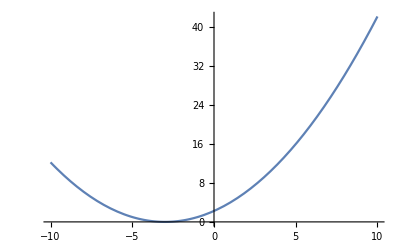

```mathematica
Plot[Abs[(x+3)/2]^2,{x,-10,10}]
```

```mathematica
FullSimplify[D[1/2 (1+BetaRegularized[(κ Abs[(x-μ)/σ]^α)/(1+ κ Abs[(x-μ)/σ]^α),1/α,1/(α κ)]),x],-∞<μ<∞&&0<σ<∞&&0<α<2]
```

(α (κ/(κ+σ^α (1/Abs[x-μ])^α))^(1/α) (1/(1+κ Abs[(x-μ)/σ]^α))^(1/(α κ)) Abs'[(x-μ)/σ])/(2 Abs[x-μ] Beta[1/α,1/(α κ)])

Can the form of the expression be further simplified by moving negative sign to a or b parameter of incomplete beta function?  t has form of 1/u

```mathematica
t has form of 1/u
```

```mathematica
1-1/u=(u-1)/u
```

```mathematica
t has the form of -1/u
```

```mathematica
1+1/u=(1+u)/u
```

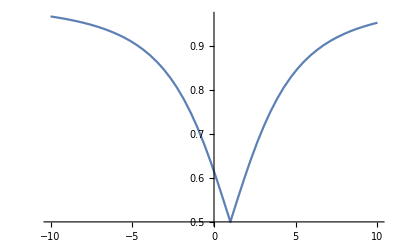

```mathematica
Plot[1/2 (1+BetaRegularized[(κ Abs[(x-μ)/σ]^α)/(1+ κ Abs[(x-μ)/σ]^α),1/α,1/(α κ)])/.{α->2,μ->1,σ->3,κ->0.5},{x,-10,10}]
```

```mathematica
Piecewise[{{1/2 BetaRegularized[ν/(x^2+ν),ν/2,1/2], x≤0}, {1/2 (1+BetaRegularized[x^2/(x^2+ν),1/2,ν/2]), True}}]
```

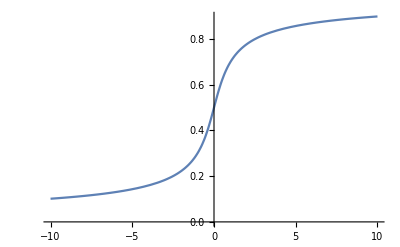

```mathematica
Plot[Piecewise[{{1/2 BetaRegularized[ν/(x^2+ν),ν/2,1/2], x≤0}, {1/2 (1+BetaRegularized[x^2/(x^2+ν),1/2,ν/2]), True}}]/.{α->2,μ->1,σ->3,ν->0.5},{x,-10,10}]
```

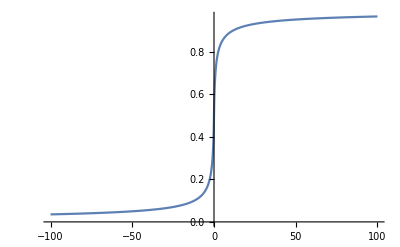

```mathematica
Plot[Piecewise[{{1/2 BetaRegularized[ν/(Abs[x]^α+ν),ν/α,1/α], x≤0}, {1/2 (1+BetaRegularized[x^α/(Abs[x]^α+ν),1/α,ν/α]), True}}]/.{α->1,μ->1,σ->3,ν->0.5},{x,-100,100}]
```

```mathematica
(α (1/(1+x^α κ))^(1/(α κ)) ((x^α κ)/(1+x^α κ))^(1/α))/(2 x Beta[1/α,1/(α κ)])
```

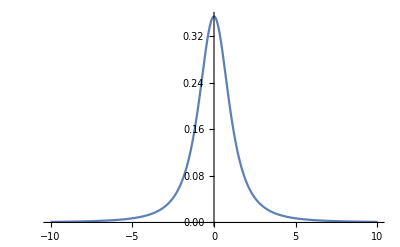

```mathematica
Plot[(α (1/(1+x^α κ))^(1/(α κ)) (κ/(1+x^α κ))^(1/α))/(2  Beta[1/α,1/(α κ)])/.{α->2,μ->1,σ->3,κ->0.5},{x,-10,10},PlotRange->Full]
```

### Work on qstatistics coupled statistics parameter comparison

```mathematica
DirValues=FullSimplify@(x D[PDF[CoupledExponentialDistribution[0,σ,κ],x],{x,1}])/PDF[CoupledExponentialDistribution[0,σ,κ],x]/.x->{σ,σ/(1+κ)};
```

```mathematica
%231
```

{(σ (Piecewise[{{{-1/(ⅇ σ^2),-ⅇ^(-1/(1+κ))/σ^2}, κ==0&&{σ,σ/(1+κ)}>0&&σ≠0}, {{-(1+κ)^(1-1/κ)/(σ+κ σ)^2,-((1+κ) (1+κ/(1+κ))^(-1/κ))/(σ+(κ σ)/(1+κ))^2}, (κ≥0||{κ (σ+κ σ),κ (σ+(κ σ)/(1+κ))}<0)&&{σ,σ/(1+κ)}>0&&{σ (σ+κ σ),σ (σ+(κ σ)/(1+κ))}>0}, {0, True}}]))/Piecewise[{{1/(σ If[{1+κ,1+κ/(1+κ)}>0,If[κ≠0,(1+(κ {σ,σ/(1+κ)})/σ)^((1+1 κ)/κ),Exp[{σ,σ/(1+κ)}/σ]],If[(1+1 κ)/κ>0,0,∞]]), {σ,σ/(1+κ)}>0&&{σ-If[κ≥0,∞,-σ/κ+0],σ/(1+κ)-If[κ≥0,∞,-σ/κ+0]}<0}, {0, True}}],(σ (Piecewise[{{{-1/(ⅇ σ^2),-ⅇ^(-1/(1+κ))/σ^2}, κ==0&&{σ,σ/(1+κ)}>0&&σ≠0}, {{-(1+κ)^(1-1/κ)/(σ+κ σ)^2,-((1+κ) (1+κ/(1+κ))^(-1/κ))/(σ+(κ σ)/(1+κ))^2}, (κ≥0||{κ (σ+κ σ),κ (σ+(κ σ)/(1+κ))}<0)&&{σ,σ/(1+κ)}>0&&{σ (σ+κ σ),σ (σ+(κ σ)/(1+κ))}>0}, {0, True}}]))/((1+κ) (Piecewise[{{1/(σ If[{1+κ,1+κ/(1+κ)}>0,If[κ≠0,(1+(κ {σ,σ/(1+κ)})/σ)^((1+1 κ)/κ),Exp[{σ,σ/(1+κ)}/σ]],If[(1+1 κ)/κ>0,0,∞]]), {σ,σ/(1+κ)}>0&&{σ-If[κ≥0,∞,-σ/κ+0],σ/(1+κ)-If[κ≥0,∞,-σ/κ+0]}<0}, {0, True}}]))}

```mathematica
%232//.{κ->0.5,σ->2}//FullSimplify
```

{(2 (Piecewise[{{{-0.0740741,-0.118652}, {2,1.33333}>0&&{6.,5.33333}>0}, {0, True}}]))/Piecewise[{{{0.148148,0.210938}, {2,1.33333}>0&&{-∞,-∞}<0&&{1.5,1.33333}>0}, {ComplexInfinity, {2,1.33333}>0&&{-∞,-∞}<0}, {0, True}}],(1.33333 (Piecewise[{{{-0.0740741,-0.118652}, {2,1.33333}>0&&{6.,5.33333}>0}, {0, True}}]))/Piecewise[{{{0.148148,0.210938}, {2,1.33333}>0&&{-∞,-∞}<0&&{1.5,1.33333}>0}, {ComplexInfinity, {2,1.33333}>0&&{-∞,-∞}<0}, {0, True}}]}

```mathematica
FullSimplify[(x D[PDF[CoupledExponentialDistribution[0,σ,κ],x],{x,1}])/PDF[CoupledExponentialDistribution[0,σ,κ],x],0<κ<∞&&0<σ<∞&&0<x<∞]/.{κ->0.5,σ->2}
```

-(1.5 x)/(2+0.5 x)

```mathematica
%241/.x->({σ,σ/(1+κ)}/.{κ->0.5,σ->2})//FullSimplify
```

{-1.,-0.75}

```mathematica
FullSimplify[D[FullSimplify[PDF[CoupledNormalDistribution[0,σ,κ],x],
0<κ<∞&&0<σ<∞&&x∈Reals],
{x,1}]]/.x->{1/√scaleShapeToBeta[σ,κ],σ,σ/√(1+2κ)}
```

{-(2 √(2/π) κ Gamma[1/2 (3+1/κ)])/(√((1+(2 κ)/(1+κ))^(1+1/κ)/κ) √((1+κ)/σ^2) σ (σ^2+(2 κ σ^2)/(1+κ)) Gamma[1/(2 κ)]),-(2 κ Gamma[1/2 (3+1/κ)])/(√π √((1+κ)^(1+1/κ)/κ) (σ^2+κ σ^2) Gamma[1/(2 κ)]),-(2 κ Gamma[1/2 (3+1/κ)])/(√π √(1+2 κ) √((1+κ/(1+2 κ))^(1+1/κ)/κ) (σ^2+(κ σ^2)/(1+2 κ)) Gamma[1/(2 κ)])}

### Examine Survival Function of Coupled Distribution

```mathematica
SFCoupledDistribution[σ,0,σ,κ,α]
```

1/2 (1-BetaRegularized[(κ σ^2)/(1+κ),1/α,1/(α κ)])

```mathematica
(x D[SFCoupledDistribution[x,μ,σ,κ,α],{x,1}])/D[SFCoupledDistribution[x,μ,σ,κ,α],{x,1}]//FullSimplify
```

x

```mathematica
Limit[1/2 (1+BetaRegularized[(κ x^α)/(1+κ Abs[(x-μ)/σ]^α),1/α,1/(α κ)])/.{κ->1,μ->0,σ->1},x->∞]
```

$Aborted

```mathematica
Abs'[x]
```

Abs'[x]

```mathematica
Clear[α]
```

General::munfl: Exp[-6.78595×10^7] is too small to represent as a normalized machine number; precision may be lost.

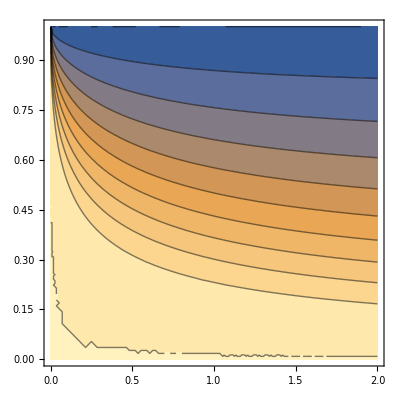

```mathematica
ContourPlot[BetaRegularized[1/2,1/α,1/(α κ)],{α,0,2},{κ,0,1}]
```

```mathematica
PDF[CoupledNormalDistribution[0,σ,0],x]
```

1/(√(ⅇ^(x^2/σ^2)) √(2 π) σ)

```mathematica
Limit[PDF[CoupledNormalDistribution[0,σ,0],x],κ->0]
```

1/(√(ⅇ^(x^2/σ^2)) √(2 π) σ)

```mathematica
?α
```

```mathematica
α
```

α

```mathematica
?CoupledDistribution
```

```mathematica
Series[Piecewise[{{1/2 BetaRegularized[1/(1+κ Abs[(x-0)/σ]^α),1/(α κ),1/α], Abs[(x-0)/σ]≤0}, {1/2 (1+BetaRegularized[(κ Abs[(x-0)/σ]^α)/(1+κ Abs[(x-0)/σ]^α),1/α,1/(α κ)]), True}}],{x,0,5}]
```

Series[Piecewise[{{1/2 BetaRegularized[1/(1+κ Abs[x/σ]^α),1/(α κ),1/α], Abs[x/σ]≤0}, {1/2 (1+BetaRegularized[(κ Abs[x/σ]^α)/(1+κ Abs[x/σ]^α),1/α,1/(α κ)]), True}}],{x,0,5}]

```mathematica
Limit[Piecewise[{{1/2 BetaRegularized[1/(1+κ Abs[(x-μ)/σ]^α),1/(α κ),1/α], Abs[(x-μ)/σ]≤0}, {1/2 (1+BetaRegularized[(κ Abs[(x-μ)/σ]^α)/(1+κ Abs[(x-μ)/σ]^α),1/α,1/(α κ)]), True}}],κ->0]
```

lim_(κ→0) (Piecewise[{{1/2 BetaRegularized[1/(1+κ Abs[(x-μ)/σ]^α),1/(α κ),1/α], Abs[(x-μ)/σ]≤0}, {1/2 (1+BetaRegularized[(κ Abs[(x-μ)/σ]^α)/(1+κ Abs[(x-μ)/σ]^α),1/α,1/(α κ)]), True}}])

```mathematica
D[Piecewise[{{1/2 BetaRegularized[1/(1+κ Abs[(x-μ)/σ]^α),1/(α κ),1/α], Abs[(x-μ)/σ]≤0}, {1/2 (1+BetaRegularized[(κ Abs[(x-μ)/σ]^α)/(1+κ Abs[(x-μ)/σ]^α),1/α,1/(α κ)]), True}}],{x,1}]//FullSimplify
```

Piecewise[{{(α (κ/(κ+Abs[(x-μ)/σ]^-α))^(1/α) (1/(1+κ Abs[(x-μ)/σ]^α))^(1/(α κ)) Abs[σ] Abs'[(x-μ)/σ])/(2 σ Abs[x-μ] Beta[1/α,1/(α κ)]), Abs[(x-μ) σ]>0}, {-(α (1/(1+κ Abs[(x-μ)/σ]^α))^(1/(α κ)) (1-1/(1+κ Abs[(x-μ)/σ]^α))^(1/α) Abs[σ/(x-μ)] Abs'[(x-μ)/σ])/(2 σ Beta[1/(α κ),1/α]), True}}]

```mathematica
Limit[Piecewise[{{(α (κ/(κ+Abs[(x-μ)/σ]^-α))^(1/α) (1/(1+κ Abs[(x-μ)/σ]^α))^(1/(α κ)) Abs[σ] Abs'[(x-μ)/σ])/(2 σ Abs[x-μ] Beta[1/α,1/(α κ)]), Abs[(x-μ) σ]>0}, {-(α (1/(1+κ Abs[(x-μ)/σ]^α))^(1/(α κ)) (1-1/(1+κ Abs[(x-μ)/σ]^α))^(1/α) Abs[σ/(x-μ)] Abs'[(x-μ)/σ])/(2 σ Beta[1/(α κ),1/α]), True}}],x->0]
```

lim_(x→0) (Piecewise[{{(α (κ/(κ+Abs[(x-μ)/σ]^-α))^(1/α) (1/(1+κ Abs[(x-μ)/σ]^α))^(1/(α κ)) Abs[σ] Abs'[(x-μ)/σ])/(2 σ Abs[x-μ] Beta[1/α,1/(α κ)]), Abs[(x-μ) σ]>0}, {-(α (1/(1+κ Abs[(x-μ)/σ]^α))^(1/(α κ)) (1-1/(1+κ Abs[(x-μ)/σ]^α))^(1/α) Abs[σ/(x-μ)] Abs'[(x-μ)/σ])/(2 σ Beta[1/(α κ),1/α]), True}}])

Simplify when near mu

```mathematica
(α (κ)^(1/α))/(2 σ^2  Beta[1/α,1/(α κ)])
```

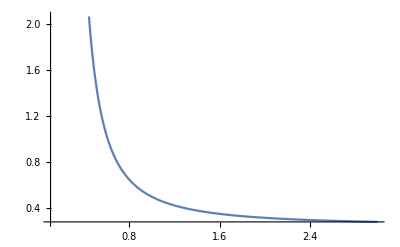

Plot::plln: Limiting value {0.01,1000} in {x,{0.01,1000},{1/100000,10}} is not a machine-sized real number.

General::stop: Further output of Plot::plln will be suppressed during this calculation.

```mathematica
Plot[(α (1)^(1/α))/(2 1^2  Beta[1/α,1/(α 1)]),{α,0.1,3}]
```

```mathematica
2Integrate[((1+κ (x/σ)^α)^(1+1/κ))^-α,{x,0,∞},Assumptions->0<α<∞&&0<κ<∞&&0<σ<∞]
```

2 Integrate[((1+κ (x/σ)^α)^(1+1/κ))^-α,{x,0,∞},Assumptions→0<α<∞&&0<κ<∞&&0<σ<∞]

```mathematica
2Integrate[((1+κ (x/σ)^α)^(1+1/κ))^-α,{x,0,σ/κ^(1/α)},Assumptions->0<α<∞&&-1<κ<0&&0<σ<∞]
```

2 κ^(-1/α) (1+κ (κ^(-1/α))^α) ((1+κ (κ^(-1/α))^α)^(1+1/κ))^-α σ Hypergeometric2F1[1,1+1/α-(α (1+κ))/κ,1+1/α,(ⅇ^(-(ⅈ π)/α))^α]

```mathematica
Solve[(CoupledExponential[((x-0)/σ)^α,κ,1])^-α==0,x,Assumptions->0<α<∞&&-1<κ<0&&0<σ<∞]
```

{}

```mathematica
FullSimplify[(CoupledExponential[((x-0)/σ)^α,κ,1])^-α,Assumptions->0<α<∞&&-1<κ<0&&0<σ<∞]
```

Piecewise[{{((1+κ (x/σ)^α)^(1+1/κ))^-α, κ (x/σ)^α>-1}, {Indeterminate, True}}]